```mathematica
CurrentValue[$FrontEnd,"NotebookAutoSave"]=True
```

True

## Neural network approximation of Bessel[1, x]

### Comparison of the root mean square error (or deviation) using the following training and validation sets

#### Training and validation data

```mathematica
dataBessel = (# -> BesselJ[1, #]) &@ RandomReal[{-8, 8}, 100000];
validationBessel = (# -> BesselJ[1, #]) &@ RandomReal[{-8, 8}, 200];
```

#### My metric

```mathematica
$refRange = Range[-8, 8, 0.001];
$refValues=BesselJ[1, $refRange];
$myMetric={};
```

#### Tanh Neural Network for Bessel Function

```mathematica
tanhNet = NetInitialize @ NetChain[{LinearLayer[30], Tanh, LinearLayer[20], Tanh, LinearLayer[1]}, "Input"->"Real", "Output"->NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[$myMetric]
```

```mathematica
{trainedTanhNet,validationLossList,batchLossList}=NetTrain[tanhNet, dataBessel,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationBessel,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->500,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

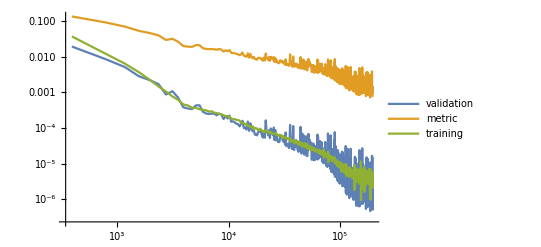

```mathematica
ListLinePlot[{validationLossList,$myMetric,Transpose[{Range[Length[#]]*validationLossList[[1,1]],#}& @Mean[Transpose@Partition[batchLossList,validationLossList[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
besselTanhRMSE = RootMeanSquare[(trainedTanhNet[#] - BesselJ[1, #]) &@ $refRange]
```

0.000714047

#### Gaussian Neural Network for Bessel Function

```mathematica
gaussNet = NetInitialize @ NetChain[{ LinearLayer[20], ElementwiseLayer[1/E^(# ^2/2)&], LinearLayer[10], ElementwiseLayer[1/E^(#^2/2)&],  LinearLayer[1]}, "Input" -> "Real", "Output" -> NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[$myMetric]
```

```mathematica
Clear[trainedGaussNet]
```

```mathematica
{trainedGaussNet,validationLossListG,batchLossListG}=NetTrain[gaussNet, dataBessel,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationBessel,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->500,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

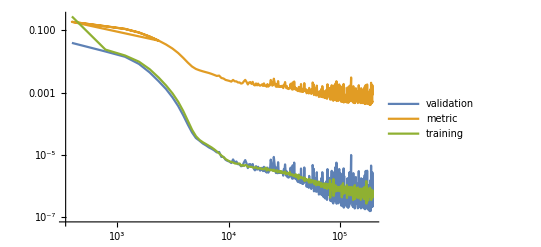

```mathematica
ListLinePlot[{validationLossListG,$myMetric,Transpose[{Range[Length[#]]*validationLossListG[[1,1]],#}& @Mean[Transpose@Partition[batchLossListG,validationLossListG[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
besselGaussRMSE = RootMeanSquare[(trainedGaussNet[#] - BesselJ[1, #]) &@ $refRange]
```

0.000403094

#### Sinusoidal Neural Network for Bessel function

```mathematica
sinNet = NetInitialize @ NetChain[{LinearLayer[30], Sin, LinearLayer[20], Sin, LinearLayer[1]}, "Input" -> "Real", "Output" ->  NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[trainedSinNet]
```

```mathematica
{trainedSinNet,validationLossListS,batchLossListS}=NetTrain[sinNet, dataBessel,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationBessel,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->500,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

```mathematica
ListLinePlot[{validationLossListS,$myMetric,Transpose[{Range[Length[#]]*validationLossListS[[1,1]],#}& @Mean[Transpose@Partition[batchLossListS,validationLossListS[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

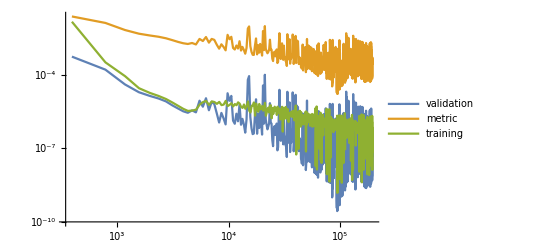
```mathematica
-Graphics-.12.12
```

```mathematica
besselSinRMSE = RootMeanSquare[(trainedSinNet[#] - BesselJ[1, #]) &@ $refRange]
```

0.000016309

The sinusoidal neural network has the least root mean square error, so we will try to analyse it further.

### Comparison of performance of sinusoidal neural net using varying datasets

```mathematica
dataBessel1 = (# -> BesselJ[1, #]) &@ RandomReal[{-8, 8}, 10000];
```

```mathematica
dataBessel2 - (# -> BesselJ[1, #]) &@ RandomReal[{-8, 8}, 50000];
```

```mathematica
dataBessel3 = (# -> BesselJ[1, #]) &@ RandomReal[{-8, 8}, 100000];
```

```mathematica
dataBessel4 = (# -> BesselJ[1, #]) &@ RandomReal[{-8, 8}, 500000];
```

```mathematica
dataBessel5 = (# -> BesselJ[1, #]) &@ RandomReal[{-8, 8}, 1000000];
```

```mathematica
Clear[trainedSinNet]
trainedSinNet = NetTrain[sinNet, dataBessel1, ValidationSet->validationBessel, MaxTrainingRounds->500]
```

NetChain[]

```mathematica
besselSinRMSE1 = RootMeanSquare[trainedSinNet[#] &@ $refRange - $refValues]
```

0.000191074

```mathematica
Clear[trainedSinNet]
trainedSinNet = NetTrain[sinNet, dataBessel2, ValidationSet->validationBessel, MaxTrainingRounds->500]
```

NetChain[]

```mathematica
besselSinRMSE2 = RootMeanSquare[trainedSinNet[#] &@ $refRange - $refValues]
```

0.0000561283

```mathematica
Clear[trainedSinNet]
trainedSinNet = NetTrain[sinNet, dataBessel3, ValidationSet->validationBessel, MaxTrainingRounds->500]
```

NetChain[]

```mathematica
besselSinRMSE3 = RootMeanSquare[trainedSinNet[#] &@ $refRange - $refValues]
```

0.000039197

```mathematica
Clear[trainedSinNet]
trainedSinNet = NetTrain[sinNet, dataBessel4, ValidationSet->validationBessel, MaxTrainingRounds->500]
```

NetChain[]

```mathematica
besselSinRMSE4 = RootMeanSquare[trainedSinNet[#] &@ $refRange - $refValues]
```

0.0000224899

```mathematica
Clear[trainedSinNet]
trainedSinNet = NetTrain[sinNet, dataBessel5, ValidationSet->validationBessel, MaxTrainingRounds->500]
```

NetChain[]

```mathematica
besselSinRMSE5 = RootMeanSquare[trainedSinNet[#] &@ $refRange - $refValues]
```

0.0000168585

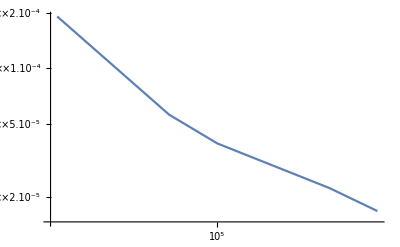

```mathematica
ListLinePlot[{{10000,besselSinRMSE1}, {50000,besselSinRMSE2}, {100000,besselSinRMSE3}, {500000,besselSinRMSE4}, {1000000,besselSinRMSE5}}, ScalingFunctions->{"Log10", "Log10"}]
```

This plot suggests that the error decreases almost exponentially with increasing training data..12

## Neural network approximation of a rational polynomial function

Consider the polynomial 1 + x + 2 x^2 + 3 x^3 + 4 x^4 + 5 x^5.

```mathematica
dataRational = (# -> 1 + Sum[i * #^i, {i, 1, 6}]) &@ RandomReal[{-8, 8}, 100000];
```

```mathematica
validationRational = (# -> 1 + Sum[i * #^i, {i, 1, 6}]) &@ RandomReal[{-8, 8}, 200];
```

#### My metric

```mathematica
$refRange = Range[-8, 8, 0.001];
$refValues= 1 + Sum[i * $refRange^i, {i, 1, 6}];
Clear[$myMetric]
$myMetric={};
```

#### Ramp Neural Network for Rational function

```mathematica
rampNet = NetInitialize @ NetChain[{LinearLayer[30], Ramp, LinearLayer[20], Ramp, LinearLayer[1]}, "Input" -> "Real", "Output" ->  NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[trainedRampNet]
```

```mathematica
{trainedRampNet,validationLossList,batchLossList}=NetTrain[rampNet, dataRational,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationRational,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->500,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

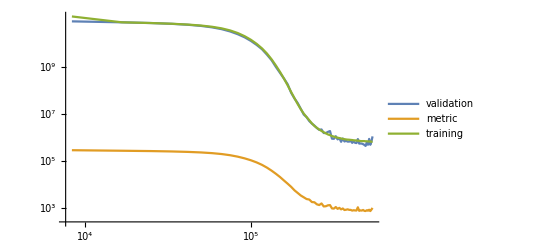

```mathematica
ListLinePlot[{validationLossList,$myMetric,Transpose[{Range[Length[#]]*validationLossList[[1,1]],#}& @Mean[Transpose@Partition[batchLossList,validationLossList[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
rationalRampRMSE = RootMeanSquare[trainedRampNet[#] &@ $refRange - $refValues]
```

766.294

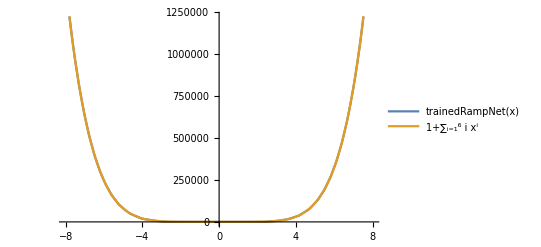

```mathematica
Plot[{trainedRampNet[x], 1 + Sum[i * x^i, {i, 1, 6}]}, {x, -8, 8}, PlotLegends->"Expressions"]
```

Let .12us now restrict the domain to positive real numbers.

```mathematica
dataRational = (# -> 1 + Sum[i * #^i, {i, 1, 6}]) &@ RandomReal[{0, 8}, 100000];
```

```mathematica
validationRational = (# -> 1 + Sum[i * #^i, {i, 1, 6}]) &@ RandomReal[{0, 8}, 200];
```

#### My metric

```mathematica
$refRange = Range[0, 8, 0.001];
$refValues= 1 + Sum[i * $refRange^i, {i, 1, 6}];
```

```mathematica
Clear[$myMetric]
$myMetric={};
```

```mathematica
Clear[trainedRampNet, validationLossList, batchLossList]
```

```mathematica
{trainedRampNet,validationLossList,batchLossList}=NetTrain[rampNet, dataRational,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationRational,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->500,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

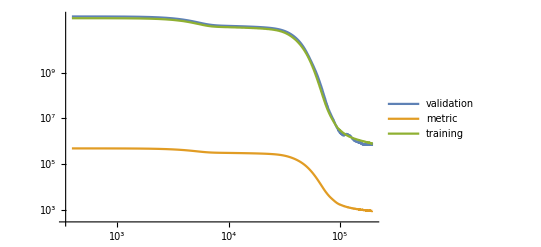

```mathematica
ListLinePlot[{validationLossList,$myMetric,Transpose[{Range[Length[#]]*validationLossList[[1,1]],#}& @Mean[Transpose@Partition[batchLossList,validationLossList[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
rationalRampRMSE = RootMeanSquare[trainedRampNet[#] &@ $refRange - $refValues]
```

982.475

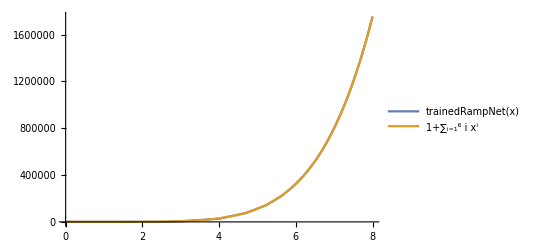

```mathematica
Plot[{trainedRampNet[x], 1 + Sum[i * x^i, {i, 1, 6}]}, {x, 0, 8}, PlotLegends->"Expressions"]
```

```mathematica
.12Soft Exponential Neural Net for Rational function
```

```mathematica
softExpNet = NetInitialize @ NetChain[{LinearLayer[30], Log, LinearLayer[20], Exp, LinearLayer[1]}, "Input" -> "Real", "Output" -> NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[trainedSoftExpNet, validationLossList, batchLossList]
```

```mathematica
{trainedSoftExpNet,validationLossList,batchLossList}=NetTrain[rampNet, dataRational,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationRational,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->500,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

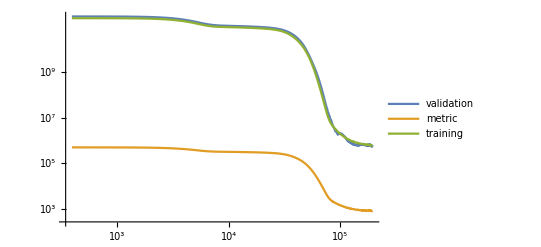

```mathematica
ListLinePlot[{validationLossList,$myMetric,Transpose[{Range[Length[#]]*validationLossList[[1,1]],#}& @Mean[Transpose@Partition[batchLossList,validationLossList[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
rationalSoftExpRMSE = RootMeanSquare[trainedRampNet[#] &@ $refRange - $refValues]
```

982.475

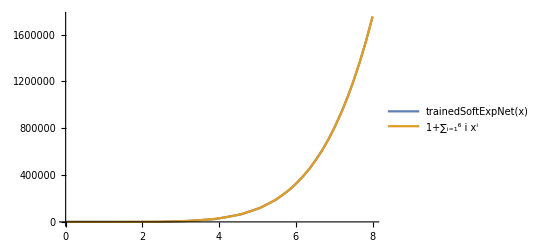

```mathematica
Plot[{trainedSoftExpNet[x], 1 + Sum[i * x^i, {i, 1, 6}]}, {x, 0, 8}, PlotLegends->"Expressions"]
```

This is rather surprising! Despite the huge error both the networks give an almost exact approximation of the rational polynomial.